# Wolfram Mathematica 在数学物理方法课程中的应用

## 1.Mathematica 基础知识

### 1.1 进行输入和计算

```mathematica
1+1
```

2

```mathematica
Sqrt[%]
```

√2

```mathematica
N[%2]
```

1.41421

### 1.3 数与数学常数

```mathematica
Sqrt[3]
```

√3

```mathematica
Sqrt[3.]
```

1.73205

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
3.1`30+2.1`20+1
```

6.2

```mathematica
E^(1+Pi I)
```

-ⅇ

### 1.5 Mathematica 中的函数

```mathematica
f[x_]:=x^2
```

```mathematica
f[a]
```

a^2

```mathematica
g[x_,y_]:=x y
```

```mathematica
g[2,x]
```

2 x

### 1.6 Mathematica 中变量的清除

```mathematica
x=1;
Integrate[x Sin[x],x]
```

Integrate::ilim: 1 中有无效的积分变量或者极限值.

∫Sin[1]ⅆ1

```mathematica
Clear[x];
Integrate[x Sin[x],x]
```

-x Cos[x]+Sin[x]

## 2 Mathematica 的语言结构

```mathematica
FullForm[Hold[f[x_]:=x^2]]
```

Hold[SetDelayed[f[Pattern[x,Blank[]]],Power[x,2]]]

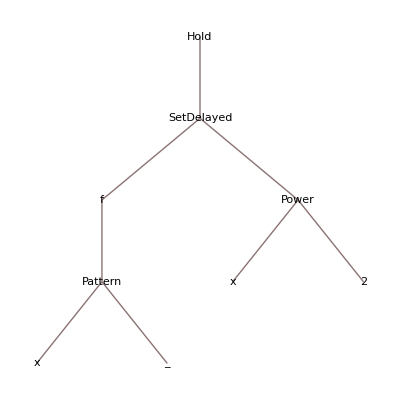

```mathematica
TreeForm[Hold[f[x_]:=x^2]]
```

```mathematica
FullForm[Hold[a=2;b=3;a+b]]
```

Hold[CompoundExpression[Set[a,2],Set[b,3],Plus[a,b]]]

```mathematica
FullForm[Hold[{1,2,3,4,5}[[2;;3]]]]
```

Hold[Part[List[1,2,3,4,5],Span[2,3]]]

```mathematica
FullForm[Plot[Sin[x],{x,0,2 Pi}]]
```

Graphics[Annotation[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[2]],Line[List[List[1.28228×10^-7,1.28228×10^-7],List[0.00192717,0.00192716],List[0.0038542,0.00385419],List[0.00770828,0.0077082],List[0.0154164,0.0154158],List[0.0308327,0.0308278],List[0.0616653,0.0616262],List[0.123331,0.123018],List[0.257035,0.254214],List[0.381879,0.372665],List[0.504274,0.483172],List[0.637043,0.594821],List[0.760951,0.68961],List[0.895233,0.780355],List[0.897293,0.781642],List[0.899353,0.782925],List[0.903473,0.785481],List[0.911713,0.790554],List[0.928192,0.800538],List[0.96115,0.819851],List[1.02707,0.855785],List[1.02899,0.856778],List[1.03091,0.857767],List[1.03475,0.859736],List[1.04244,0.863636],List[1.05781,0.871283],List[1.08855,0.885957],List[1.09047,0.886846],List[1.0924,0.887733],List[1.09624,0.889495],List[1.10393,0.892981],List[1.1193,0.899794],List[1.15004,0.91278],List[1.15212,0.913629],List[1.15421,0.914474],List[1.15837,0.916153],List[1.16671,0.919461],List[1.18338,0.925887],List[1.21671,0.937965],List[1.2188,0.938685],List[1.22088,0.939402],List[1.22505,0.940822],List[1.23338,0.943614],List[1.25005,0.949],List[1.28339,0.958981],List[1.28533,0.959531],List[1.28728,0.960077],List[1.29117,0.961158],List[1.29895,0.963276],List[1.31451,0.967338],List[1.31645,0.967829],List[1.3184,0.968316],List[1.32229,0.969281],List[1.33007,0.971165],List[1.34563,0.974757],List[1.34758,0.975189],List[1.34952,0.975618],List[1.35341,0.976465],List[1.36119,0.978113],List[1.37675,0.981232],List[1.3787,0.981606],List[1.38064,0.981975],List[1.38453,0.982703],List[1.39231,0.984114],List[1.40787,0.986757],List[1.40978,0.987065],List[1.41169,0.987369],List[1.4155,0.987966],List[1.42313,0.989117],List[1.42504,0.989396],List[1.42694,0.989671],List[1.43076,0.99021],List[1.43838,0.991246],List[1.44029,0.991496],List[1.4422,0.991742],List[1.44601,0.992224],List[1.45364,0.993145],List[1.46889,0.994812],List[1.4708,0.995004],List[1.47271,0.995193],List[1.47652,0.995559],List[1.48415,0.996248],List[1.48605,0.996412],List[1.48796,0.996571],List[1.49177,0.996879],List[1.4994,0.997452],List[1.50131,0.997587],List[1.50322,0.997717],List[1.50703,0.997968],List[1.50894,0.998087],List[1.51084,0.998203],List[1.51466,0.998425],List[1.51656,0.99853],List[1.51847,0.998631],List[1.52228,0.998824],List[1.52419,0.998914],List[1.5261,0.999001],List[1.52991,0.999164],List[1.53198,0.999247],List[1.53405,0.999325],List[1.53612,0.999399],List[1.53819,0.999468],List[1.54026,0.999534],List[1.54232,0.999595],List[1.54646,0.999704],List[1.54853,0.999752],List[1.5506,0.999796],List[1.55267,0.999836],List[1.55474,0.999871],List[1.55681,0.999902],List[1.55888,0.999929],List[1.56095,0.999951],List[1.56301,0.99997],List[1.56508,0.999984],List[1.56715,0.999993],List[1.56922,0.999999],List[1.57129,1.],List[1.57336,0.999997],List[1.57543,0.999989],List[1.5775,0.999978],List[1.57957,0.999962],List[1.58163,0.999941],List[1.5837,0.999917],List[1.58577,0.999888],List[1.58784,0.999855],List[1.58991,0.999817],List[1.59198,0.999776],List[1.59405,0.99973],List[1.59612,0.999679],List[1.59819,0.999625],List[1.60025,0.999566],List[1.60232,0.999503],List[1.60439,0.999436],List[1.60646,0.999364],List[1.60853,0.999288],List[1.61267,0.999123],List[1.61474,0.999035],List[1.61681,0.998942],List[1.62094,0.998743],List[1.62922,0.998294],List[1.63129,0.998171],List[1.63336,0.998044],List[1.6375,0.997776],List[1.64577,0.997191],List[1.64784,0.997034],List[1.64991,0.996872],List[1.65405,0.996537],List[1.66232,0.995814],List[1.66425,0.995636],List[1.66618,0.995454],List[1.67004,0.995079],List[1.67777,0.994284],List[1.6797,0.994076],List[1.68163,0.993864],List[1.68549,0.99343],List[1.69321,0.992517],List[1.69514,0.992279],List[1.69707,0.992038],List[1.70093,0.991544],List[1.70865,0.990513],List[1.7241,0.988272],List[1.72603,0.987976],List[1.72796,0.987675],List[1.73182,0.987064],List[1.73954,0.985796],List[1.75499,0.983085],List[1.78587,0.97696],List[1.78797,0.976511],List[1.79006,0.976058],List[1.79424,0.975139],List[1.80261,0.97325],List[1.81936,0.969268],List[1.85284,0.96049],List[1.85493,0.959905],List[1.85702,0.959316],List[1.86121,0.958126],List[1.86958,0.955696],List[1.88632,0.950635],List[1.9198,0.939714],List[1.92185,0.93901],List[1.92391,0.938301],List[1.92802,0.936873],List[1.93623,0.933968],List[1.95267,0.927969],List[1.98554,0.915221],List[2.05128,0.886774],List[2.05319,0.885887],List[2.05511,0.884996],List[2.05894,0.883206],List[2.0666,0.879586],List[2.08193,0.872191],List[2.11258,0.856789],List[2.17389,0.823584],List[2.17597,0.822404],List[2.17805,0.82122],List[2.1822,0.818841],List[2.19051,0.814042],List[2.20714,0.804275],List[2.24039,0.784076],List[2.30688,0.741103],List[2.43101,0.652275],List[2.56551,0.54474],List[2.69757,0.429578],List[2.82076,0.315355],List[2.95433,0.186171],List[3.07904,0.0625152],List[3.2013,-0.0596671],List[3.33393,-0.191151],List[3.4577,-0.310869],List[3.59185,-0.435193],List[3.72354,-0.549654],List[3.84638,-0.647871],List[3.97959,-0.743305],List[3.98153,-0.744603],List[3.98348,-0.745899],List[3.98736,-0.748481],List[3.99513,-0.753613],List[4.01068,-0.763738],List[4.04176,-0.783434],List[4.10394,-0.820535],List[4.10584,-0.821623],List[4.10775,-0.822707],List[4.11156,-0.824866],List[4.11918,-0.82915],List[4.13442,-0.837571],List[4.16489,-0.853829],List[4.1668,-0.854819],List[4.1687,-0.855806],List[4.17251,-0.85777],List[4.18013,-0.861662],List[4.19537,-0.869294],List[4.22584,-0.883952],List[4.22791,-0.884917],List[4.22997,-0.885877],List[4.23411,-0.887787],List[4.24238,-0.891562],List[4.25891,-0.898928],List[4.29198,-0.912921],List[4.29405,-0.913763],List[4.29611,-0.914601],List[4.30025,-0.916264],List[4.30851,-0.919545],List[4.32505,-0.925916],List[4.35812,-0.937899],List[4.36004,-0.938566],List[4.36197,-0.93923],List[4.36583,-0.940547],List[4.37354,-0.943139],List[4.38897,-0.948154],List[4.41982,-0.957507],List[4.42175,-0.958061],List[4.42368,-0.958612],List[4.42754,-0.959703],List[4.43525,-0.961842],List[4.45068,-0.965948],List[4.48153,-0.97347],List[4.48362,-0.973947],List[4.48571,-0.974419],List[4.48989,-0.97535],List[4.49825,-0.977161],List[4.51498,-0.980578],List[4.51707,-0.980986],List[4.51916,-0.981389],List[4.52334,-0.982183],List[4.5317,-0.98372],List[4.54843,-0.986588],List[4.55052,-0.986927],List[4.55261,-0.987262],List[4.55679,-0.987918],List[4.56515,-0.98918],List[4.56724,-0.989484],List[4.56933,-0.989784],List[4.57351,-0.990372],List[4.58187,-0.991495],List[4.58396,-0.991765],List[4.58605,-0.99203],List[4.59023,-0.992548],List[4.5986,-0.993533],List[4.61532,-0.995292],List[4.61727,-0.99548],List[4.61922,-0.995663],List[4.62313,-0.996019],List[4.63094,-0.996684],List[4.63289,-0.996841],List[4.63484,-0.996995],List[4.63874,-0.997289],List[4.64655,-0.997833],List[4.6485,-0.99796],List[4.65046,-0.998083],List[4.65436,-0.998317],List[4.65631,-0.998428],List[4.65826,-0.998536],List[4.66217,-0.998739],List[4.66412,-0.998835],List[4.66607,-0.998928],List[4.66998,-0.999101],List[4.67193,-0.999182],List[4.67388,-0.999259],List[4.67778,-0.999401],List[4.67974,-0.999467],List[4.68169,-0.999529],List[4.68364,-0.999587],List[4.68559,-0.999641],List[4.68754,-0.999691],List[4.6895,-0.999738],List[4.69145,-0.999781],List[4.6934,-0.99982],List[4.69535,-0.999855],List[4.6973,-0.999886],List[4.69926,-0.999914],List[4.70121,-0.999937],List[4.70316,-0.999957],List[4.70511,-0.999974],List[4.70706,-0.999986],List[4.70902,-0.999994],List[4.71097,-0.999999],List[4.71292,-1.],List[4.71487,-0.999997],List[4.71682,-0.99999],List[4.71878,-0.99998],List[4.72073,-0.999965],List[4.72268,-0.999947],List[4.72463,-0.999925],List[4.72658,-0.999899],List[4.72854,-0.99987],List[4.73049,-0.999836],List[4.73244,-0.999799],List[4.73439,-0.999758],List[4.73634,-0.999713],List[4.74025,-0.999612],List[4.74216,-0.999557],List[4.74408,-0.999498],List[4.7479,-0.999369],List[4.74982,-0.9993],List[4.75173,-0.999226],List[4.75556,-0.999068],List[4.75747,-0.998984],List[4.75939,-0.998896],List[4.76321,-0.998709],List[4.77087,-0.998291],List[4.77278,-0.998177],List[4.77469,-0.99806],List[4.77852,-0.997814],List[4.78618,-0.997279],List[4.78809,-0.997136],List[4.79,-0.996989],List[4.79383,-0.996685],List[4.80149,-0.996033],List[4.8034,-0.995861],List[4.80531,-0.995686],List[4.80914,-0.995323],List[4.8168,-0.994554],List[4.81871,-0.994353],List[4.82062,-0.994148],List[4.82445,-0.993727],List[4.83211,-0.992842],List[4.83402,-0.992612],List[4.83593,-0.992378],List[4.83976,-0.991899],List[4.84742,-0.990898],List[4.86273,-0.988721],List[4.8648,-0.988407],List[4.86688,-0.98809],List[4.87103,-0.987443],List[4.87933,-0.986097],List[4.89594,-0.983202],List[4.89802,-0.982821],List[4.90009,-0.982435],List[4.90424,-0.981652],List[4.91255,-0.980035],List[4.92915,-0.976598],List[4.93123,-0.97615],List[4.93331,-0.975697],List[4.93746,-0.974779],List[4.94576,-0.972892],List[4.96237,-0.968918],List[4.99558,-0.960169],List[4.99752,-0.959625],List[4.99945,-0.959079],List[5.00333,-0.957974],List[5.01108,-0.955723],List[5.02658,-0.951047],List[5.05758,-0.941012],List[5.05951,-0.940355],List[5.06145,-0.939694],List[5.06533,-0.938362],List[5.07308,-0.935655],List[5.08857,-0.930073],List[5.11957,-0.91824],List[5.12167,-0.917406],List[5.12377,-0.916569],List[5.12797,-0.914882],List[5.13637,-0.911459],List[5.15316,-0.904421],List[5.18676,-0.889582],List[5.25394,-0.85691],List[5.256,-0.855846],List[5.25806,-0.854778],List[5.26218,-0.852631],List[5.27043,-0.848294],List[5.28692,-0.839448],List[5.3199,-0.821072],List[5.38586,-0.781663],List[5.50892,-0.699195],List[5.64235,-0.597868],List[5.76692,-0.493638],List[5.88904,-0.38402],List[6.02154,-0.258675],List[6.14517,-0.137577],List[6.14733,-0.13544],List[6.14948,-0.133304],List[6.1538,-0.129028],List[6.16242,-0.120469],List[6.17967,-0.103326],List[6.21418,-0.0689526],List[6.21633,-0.0668011],List[6.21849,-0.0646493],List[6.2228,-0.0603447],List[6.23143,-0.0517324],List[6.24868,-0.0344969],List[6.25084,-0.0323416],List[6.25299,-0.0301862],List[6.25731,-0.0258749],List[6.26593,-0.0172511],List[6.26809,-0.0150949],List[6.27025,-0.0129386],List[6.27456,-0.00862592],List[6.27672,-0.00646951],List[6.27887,-0.00431306],List[6.28103,-0.0021566],List[6.28319,-1.28228×10^-7]]]],"Charting`Private`Tag#1"]]],List[]],Association[Rule["HighlightElements",Association[Rule["Label",List["XYLabel"]],Rule["Ball",List["InterpolatedBall"]]]],Rule["LayoutOptions",Association[Rule["PanelPlotLayout",Association[]],Rule["PlotRange",List[List[0,Times[2,Pi]],List[-1.,1.]]],Rule["Frame",List[List[False,False],List[False,False]]],Rule["AxesOrigin",List[0,0]],Rule["ImageSize",List[360,Times[360,Power[GoldenRatio,-1]]]],Rule["Axes",List[True,True]],Rule["LabelStyle",List[]],Rule["AspectRatio",Power[GoldenRatio,-1]],Rule["DefaultStyle",List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[2]]]],Rule["HighlightLabelingFunctions",Association[Rule["CoordinatesToolOptions",Function[List[Identity[Part[Slot[1],1]],Identity[Part[Slot[1],2]]]]],Rule["ScalingFunctions",List[List[Identity,Identity],List[Identity,Identity]]]]],Rule["Primitives",List[]],Rule["GCFlag",False]]],Rule["Meta",Association[Rule["DefaultHighlight",List["Dynamic",None]],Rule["Index",List[]],Rule["Function",Plot],Rule["GroupHighlight",False]]]],"DynamicHighlight"],List[Rule[DisplayFunction,Identity],Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[0,Times[2,Pi]],List[-1.,1.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.02]]]],Rule[Ticks,List[Automatic,Automatic]]]]

```mathematica
InputForm[Plot[Sin[x],{x,0,2 Pi}]]
```

Graphics[Annotation[
  {{{{}, {}, Annotation[{Directive[Opacity[1.], RGBColor[0.368417, 0.506779, 
         0.709798], AbsoluteThickness[2]], Line[{{1.2822827157509358*^-7, 
        1.2822827157509324*^-7}, {0.0019271655319089223, 
        0.001927164339004283}, {0.0038542028355462695, 0.00385419329326691}, 
        {0.007708277442820964, 0.007708201108565738}, {0.015416426657370353, 
        0.015415816004008815}, {0.030832725086469132, 0.030827840094677948}, 
        {0.06166532194466669, 0.061626247826437476}, {0.1233305156610618, 
        0.12301810194283724}, {0.2570347881802097, 0.2542138749185557}, 
        {0.3818787050494512, 0.3726645007390021}, {0.504273679847541, 
        0.4831716559080398}, {0.6370425397319885, 0.5948206667810294}, 
        {0.7609510439665297, 0.6896104843619676}, {0.8952334332874284, 
        0.7803550768254575}, {0.8972933309007058, 0.7816415498416076}, 
        {0.8993532285139831, 0.7829247062145637}, {0.9034730237405377, 
        0.7854810472663536}, {0.9117126141936469, 0.7905536910323366}, 
        {0.9281917950998653, 0.8005376246467047}, {0.961150156912302, 
        0.8198506642936907}, {1.0270668805371757, 0.855785278429456}, 
        {1.0289883350934232, 0.8567777264106476}, {1.0309097896496706, 
        0.8577670111800607}, {1.0347526987621656, 0.8597360764855387}, 
        {1.0424385169871557, 0.8636360886325238}, {1.0578101534371358, 
        0.871282836694368}, {1.088553426337096, 0.8859569678649591}, 
        {1.0904748808933435, 0.8868464399329709}, {1.092396335449591, 
        0.8877326377759202}, {1.0962392445620859, 0.8894951977114104}, 
        {1.103925062787076, 0.8929808837325072}, {1.119296699237056, 
        0.8997938037956826}, {1.1500399721370163, 0.9127802676472789}, 
        {1.152123518647738, 0.9136293123298869}, {1.15420706515846, 
        0.9144743907973655}, {1.1583741581799036, 0.9161526344296697}, 
        {1.166708344222791, 0.9194613668487993}, {1.1833767163085658, 
        0.9258870137580502}, {1.2167134604801153, 0.9379648812640387}, 
        {1.2187970069908372, 0.9386852734597927}, {1.220880553501559, 
        0.9394015906683686}, {1.2250476465230027, 0.9408219877030862}, 
        {1.23338183256589, 0.9436137462886434}, {1.2500502046516648, 
        0.9490004488089845}, {1.2833869488232146, 0.9589814532774429}, 
        {1.2853320522769067, 0.9595310149939811}, {1.2872771557305986, 
        0.9600769463956869}, {1.291167362637983, 0.9611579100063794}, 
        {1.298947776452751, 0.9632761834893663}, {1.3145086040822878, 
        0.9673376713325591}, {1.3164537075359797, 0.9678289078627277}, 
        {1.3183988109896718, 0.9683164826835982}, {1.3222890178970559, 
        0.9692806398324919}, {1.3300694317118242, 0.9711649333808123}, 
        {1.3456302593413607, 0.9747570429220562}, {1.3475753627950526, 
        0.9751894785134673}, {1.3495204662487448, 0.9756182245474039}, 
        {1.3534106731561288, 0.9764646414683034}, {1.3611910869708972, 
        0.9781131301827487}, {1.3767519146004337, 0.9812323825384774}, 
        {1.3786970180541256, 0.9816055983862323}, {1.3806421215078177, 
        0.9819751004015963}, {1.3845323284152018, 0.982702957357274}, 
        {1.3923127422299701, 0.9841140447107248}, {1.4078735698595066, 
        0.9867574189497462}, {1.409780408593337, 0.9870649196839719}, 
        {1.4116872473271673, 0.9873688314177196}, {1.415500924794828, 
        0.9879658834767021}, {1.4231282797301492, 0.9891168718422977}, 
        {1.4250351184639793, 0.989395630363058}, {1.4269419571978097, 
        0.9896707914087998}, {1.4307556346654704, 0.9902103170863328}, 
        {1.4383829896007918, 0.9912461555962515}, {1.4402898283346222, 
        0.9914961070359759}, {1.4421966670684525, 0.9917424533632795}, 
        {1.446010344536113, 0.992224327110842}, {1.4536376994714342, 
        0.9931447747237425}, {1.4688924093420768, 0.9948122874129468}, 
        {1.470799248075907, 0.9950044569152444}, {1.4727060868097372, 
        0.9951930085486457}, {1.476519764277398, 0.9955592554795967}, 
        {1.4841471192127194, 0.9962483056308926}, {1.4860539579465497, 
        0.9964115137227522}, {1.48796079668038, 0.9965710988296106}, 
        {1.4917744741480405, 0.9968793977804729}, {1.4994018290833617, 
        0.9974524952137558}, {1.501308667817192, 0.9975867039163834}, 
        {1.5032155065510224, 0.9977172853609797}, {1.5070291840186831, 
        0.9979675645900754}, {1.5089360227525135, 0.9980872614645513}, 
        {1.5108428614863438, 0.9982033292609522}, {1.5146565389540043, 
        0.998424575944621}, {1.5165633776878344, 0.9985297540274285}, 
        {1.5184702164216648, 0.9986313014232436}, {1.5222838938893255, 
        0.9988235026901806}, {1.5241907326231559, 0.9989141558624522}, 
        {1.5260975713569862, 0.9990011769500338}, {1.529911248824647, 
        0.9991643216186877}, {1.5319801795129515, 0.9992467479388707}, 
        {1.5340491102012561, 0.9993248970106624}, {1.5361180408895607, 
        0.9993987684995479}, {1.5381869715778655, 0.9994683620893222}, 
        {1.5402559022661704, 0.999533677482092}, {1.542324832954475, 
        0.9995947143982763}, {1.5464626943310842, 0.9997039517741367}, 
        {1.5485316250193888, 0.9997521517662251}, {1.5506005557076934, 
        0.9997960723465549}, {1.552669486395998, 0.9998357133271253}, 
        {1.5547384170843028, 0.9998710745382542}, {1.5568073477726077, 
        0.9999021558285789}, {1.5588762784609123, 0.9999289570650568}, 
        {1.5609452091492169, 0.9999514781329658}, {1.5630141398375215, 
        0.9999697189359052}, {1.565083070525826, 0.9999836793957958}, 
        {1.5671520012141307, 0.9999933594528801}, {1.5692209319024353, 
        0.9999987590657231}, {1.57128986259074, 0.9999998782112116}, 
        {1.573358793279045, 0.9999967168845553}, {1.5754277239673495, 
        0.9999892750992861}, {1.5774966546556541, 0.9999775528872585}, 
        {1.5795655853439587, 0.999961550298649}, {1.5816345160322633, 
        0.9999412674019562}, {1.583703446720568, 0.9999167042840006}, 
        {1.5857723774088726, 0.9998878610499239}, {1.5878413080971774, 
        0.9998547378231887}, {1.5899102387854822, 0.9998173347455782}, 
        {1.5919791694737868, 0.9997756519771952}, {1.5940481001620914, 
        0.9997296896964616}, {1.596117030850396, 0.9996794481001177}, 
        {1.5981859615387006, 0.9996249274032214}, {1.6002548922270052, 
        0.9995661278391469}, {1.6023238229153098, 0.9995030496595841}, 
        {1.6043927536036147, 0.9994356931345377}, {1.6064616842919195, 
        0.9993640585523252}, {1.608530614980224, 0.9992881462195765}, 
        {1.6126684763568333, 0.9991234896205428}, {1.614737407045138, 
        0.9990347460590658}, {1.6168063377334425, 0.9989417261566658}, 
        {1.620944199110052, 0.9987428589400763}, {1.6292199218632706, 
        0.9982938271614664}, {1.6312888525515752, 0.9981708850461833}, 
        {1.6333577832398798, 0.9980436702877108}, {1.6374956446164892, 
        0.9977764250376405}, {1.6457713673697079, 0.9971906880040196}, 
        {1.6478402980580125, 0.9970335810141968}, {1.649909228746317, 
        0.9968722062493834}, {1.6540470901229263, 0.9965366561760906}, 
        {1.662322812876145, 0.9958143743466595}, {1.6642533005074198, 
        0.9956360747050302}, {1.6661837881386945, 0.995454064545459}, 
        {1.6700447634012443, 0.9950789153995656}, {1.677766713926344, 
        0.9942841216643886}, {1.6796972015576188, 0.9940761576460222}, 
        {1.6816276891888937, 0.9938644889231839}, {1.6854886644514433, 
        0.9934300405332672}, {1.6932106149765427, 0.9925167229335421}, 
        {1.6951411026078176, 0.9922791441397993}, {1.6970715902390925, 
        0.992037867338661}, {1.7009325655016423, 0.9915442233247193}, 
        {1.7086545160267417, 0.990512599695223}, {1.7240984170769407, 
        0.9882722299515398}, {1.7260289047082156, 0.9879755986512128}, 
        {1.7279593923394905, 0.987675285381863}, {1.7318203676020403, 
        0.9870636174266212}, {1.7395423181271397, 0.9857961480515994}, 
        {1.7549862191773387, 0.9830849445640588}, {1.7858740212777366, 
        0.9769598153400458}, {1.7879666008634858, 0.9765110713568594}, 
        {1.790059180449235, 0.9760580513413295}, {1.7942443396207335, 
        0.9751391911668498}, {1.8026146579637303, 0.9732502469670653}, 
        {1.819355294649724, 0.9692679326365597}, {1.8528365680217114, 
        0.9604896062780456}, {1.8549291476074605, 0.9599051056843635}, 
        {1.8570217271932097, 0.959316401773997}, {1.8612068863647082, 
        0.9581263943330792}, {1.869577204707705, 0.9556960543090358}, 
        {1.8863178413936987, 0.9506346758110856}, {1.9197991147656859, 
        0.9397141875380657}, {1.9218534296315735, 0.9390097098112606}, 
        {1.9239077444974608, 0.9383012692680873}, {1.9280163742292356, 
        0.936872511708413}, {1.9362336336927854, 0.9339675754613147}, 
        {1.9526681526198852, 0.9279687105727975}, {1.9855371904740848, 
        0.9152207709228335}, {2.0512752661824836, 0.8867736568214569}, 
        {2.053191137991341, 0.8858865063862249}, {2.055107009800199, 
        0.8849961042481709}, {2.058938753417914, 0.883205557948632}, 
        {2.066602240653345, 0.8795855895181172}, {2.081929215124206, 
        0.8721908974026384}, {2.112583164065929, 0.8567886352600307}, 
        {2.1738910619493748, 0.8235842465112402}, {2.175969025712707, 
        0.8224038607722788}, {2.178046989476039, 0.8212199239494951}, 
        {2.182202917002703, 0.818841417516406}, {2.190514772056031, 
        0.8140420176039472}, {2.207138482162687, 0.804274835207209}, 
        {2.2403859023759995, 0.7840764676698918}, {2.306880742802624, 
        0.7411031219178127}, {2.4310100680059663, 0.6522754710746894}, 
        {2.5655132782956667, 0.5447402771484026}, {2.697567546514215, 
        0.42957772713203446}, {2.820761459082857, 0.3153554511260218}, 
        {2.954329256737857, 0.1861708352681441}, {3.0790366987429505, 
        0.06251516334017572}, {3.2012951986768923, -0.05966708417636863}, 
        {3.3339275836971916, -0.19115128932767655}, {3.4576996130675846, 
        -0.3108687742575189}, {3.5918455275243355, -0.43519321980343784}, 
        {3.7235424999099345, -0.549653867612323}, {3.846379116645627, 
        -0.6478711825589065}, {3.9795896184676773, -0.7433046755726647}, 
        {3.981532589501617, -0.7446030280816351}, {3.983475560535557, 
        -0.7458985696134667}, {3.987361502603436, -0.7484812001929632}, 
        {3.9951333867391954, -0.7536125151423854}, {4.010677155010713, 
        -0.7637382790138112}, {4.041764691553749, -0.7834338385481847}, 
        {4.103939764639821, -0.8205354257281964}, {4.105844470953899, 
        -0.8216226585479437}, {4.107749177267976, -0.8227069105987015}, 
        {4.111558589896132, -0.8248664566698257}, {4.1191774151524445, 
        -0.8291496072337002}, {4.134415065665069, -0.8375712755391325}, 
        {4.164890366690317, -0.8538292962794404}, {4.166795073004395, 
        -0.8548192476558022}, {4.168699779318473, -0.855806097829102}, 
        {4.172509191946629, -0.8577704802569843}, {4.180128017202941, 
        -0.861661873902663}, {4.195365667715565, -0.8692943895789487}, 
        {4.225840968740814, -0.8839521934370734}, {4.227907767009366, 
        -0.884916692708362}, {4.229974565277918, -0.8858774119221074}, 
        {4.234108161815023, -0.8877874937776966}, {4.242375354889233, 
        -0.8915621173125434}, {4.258909741037652, -0.8989283062064903}, 
        {4.291978513334489, -0.9129214911665804}, {4.294045311603041, 
        -0.91376307387258}, {4.2961121098715935, -0.9146007532992904}, 
        {4.300245706408699, -0.9162643880184258}, {4.308512899482908, 
        -0.9195446617800588}, {4.325047285631326, -0.9259164475524849}, 
        {4.358116057928164, -0.9378989661064421}, {4.360044413139687, 
        -0.9385661847535481}, {4.36197276835121, -0.9392299132928624}, 
        {4.365829478774255, -0.9405468901886643}, {4.373542899620345, 
        -0.9431388549606081}, {4.3889697413125255, -0.948154293060208}, 
        {4.419823424696887, -0.9575070963446649}, {4.421751779908409, 
        -0.9580614720957839}, {4.423680135119932, -0.9586122852448582}, 
        {4.427536845542977, -0.9597032155572174}, {4.435250266389067, 
        -0.9618422357239117}, {4.450677108081248, -0.9659484732670754}, 
        {4.481530791465609, -0.9734703886979993}, {4.483621238631606, 
        -0.9739465828809345}, {4.485711685797603, -0.9744185209487001}, 
        {4.489892580129597, -0.9753496205079142}, {4.498254368793584, 
        -0.9771606567479661}, {4.51497794612156, -0.9805776407913966}, 
        {4.517068393287556, -0.9809855000855563}, {4.519158840453553, 
        -0.9813890725047052}, {4.523339734785547, -0.982183349682318}, 
        {4.531701523449534, -0.9837203851951678}, {4.54842510077751, 
        -0.9865880110231746}, {4.550515547943506, -0.9869270791939445}, 
        {4.552605995109504, -0.9872618345251946}, {4.556786889441497, 
        -0.987918400836508}, {4.565148678105485, -0.9891797162821415}, 
        {4.567239125271482, -0.989484241832617}, {4.5693295724374785, 
        -0.9897844433688542}, {4.573510466769473, -0.9903718691700315}, 
        {4.58187225543346, -0.9914947761459183}, {4.583962702599457, 
        -0.9917646739089758}, {4.586053149765454, -0.9920302376923803}, 
        {4.590234044097448, -0.9925483586971543}, {4.598595832761435, 
        -0.9935325431581933}, {4.615319410089411, -0.9952924474135678}, 
        {4.6172714141983775, -0.9954797338799681}, {4.619223418307345, 
        -0.995663227251192}, {4.623127426525279, -0.9960188319258931}, 
        {4.630935442961148, -0.9966844943384429}, {4.6328874470701145, 
        -0.9968414172764121}, {4.634839451179082, -0.9969945419307571}, 
        {4.638743459397016, -0.9972893940692339}, {4.646551475832885, 
        -0.9978334942406683}, {4.648503479941851, -0.9979600153836806}, 
        {4.650455484050819, -0.9980827339808533}, {4.654359492268753, 
        -0.9983167616817821}, {4.65631149637772, -0.998428069893818}, 
        {4.6582635004866875, -0.9985355737765774}, {4.662167508704622, 
        -0.9987391669302672}, {4.664119512813588, -0.9988352554254427}, 
        {4.666071516922556, -0.9989275380398349}, {4.66997552514049, 
        -0.9991006842342673}, {4.671927529249457, -0.9991815471545655}, 
        {4.673879533358424, -0.9992586028745983}, {4.677783541576359, 
        -0.9994012915539486}, {4.679735545685325, -0.9994669239695767}, 
        {4.681687549794293, -0.9995287480975628}, {4.6836395539032605, 
        -0.9995867637023375}, {4.685591558012227, -0.9996409705628425}, 
        {4.687543562121194, -0.9996913684725326}, {4.689495566230161, 
        -0.9997379572393758}, {4.691447570339129, -0.9997807366858539}, 
        {4.693399574448096, -0.9998197066489635}, {4.695351578557062, 
        -0.9998548669802167}, {4.69730358266603, -0.9998862175456416}, 
        {4.699255586774997, -0.9999137582257822}, {4.701207590883964, 
        -0.9999374889157}, {4.703159594992931, -0.9999574095249734}, 
        {4.705111599101898, -0.9999735199776986}, {4.707063603210866, 
        -0.9999858202124895}, {4.709015607319833, -0.9999943101824783}, 
        {4.710967611428799, -0.9999989898553157}, {4.712919615537767, 
        -0.9999998592131705}, {4.714871619646734, -0.9999969182527302}, 
        {4.716823623755701, -0.9999901669852007}, {4.718775627864668, 
        -0.9999796054363067}, {4.720727631973635, -0.9999652336462909}, 
        {4.722679636082603, -0.9999470516699144}, {4.72463164019157, 
        -0.9999250595764564}, {4.726583644300536, -0.9998992574497138}, 
        {4.728535648409504, -0.9998696453880008}, {4.730487652518471, 
        -0.9998362235041489}, {4.732439656627438, -0.9997989919255063}, 
        {4.734391660736405, -0.9997579507939368}, {4.736343664845372, 
        -0.9997131002658205}, {4.7402476730633065, -0.9996119717180407}, 
        {4.742161412452412, -0.9995568338809567}, {4.744075151841518, 
        -0.9994980352695916}, {4.747902630619728, -0.9993694565987994}, 
        {4.749816370008833, -0.9992996770102786}, {4.751730109397938, 
        -0.9992262375892872}, {4.755557588176149, -0.9990683803391527}, 
        {4.757471327565255, -0.9989839630881456}, {4.75938506695436, 
        -0.9988958871609377}, {4.763212545732571, -0.9987087605815942}, 
        {4.770867503288993, -0.9982906183991543}, {4.772781242678098, 
        -0.9981769415206926}, {4.774694982067203, -0.9980596089216637}, 
        {4.778522460845414, -0.9978139782941661}, {4.786177418401836, 
        -0.9972788681968285}, {4.788091157790942, -0.9971359583355132}, 
        {4.790004897180047, -0.9969893965661247}, {4.7938323759582575, 
        -0.9966853194635711}, {4.801487333514679, -0.9960333668752152}, 
        {4.803401072903784, -0.9958612575275346}, {4.80531481229289, 
        -0.9956855009402419}, {4.8091422910711, -0.9953230486349366}, 
        {4.8167972486275215, -0.9945544063660269}, {4.818710988016627, 
        -0.9943531378725057}, {4.820624727405733, -0.9941482276627056}, 
        {4.824452206183943, -0.9937274851094541}, {4.832107163740364, 
        -0.9928423333212237}, {4.83402090312947, -0.9926119528569672}, 
        {4.835934642518575, -0.9923779370533432}, {4.839762121296785, 
        -0.991899002869539}, {4.847417078853207, -0.9908975490317617}, 
        {4.86272699396605, -0.988720509333535}, {4.86480282530963, 
        -0.988407477199899}, {4.86687865665321, -0.9880901859450845}, 
        {4.871030319340369, -0.9874428315591933}, {4.879333644714688, 
        -0.9860970747203687}, {4.895940295463326, -0.9832016996684034}, 
        {4.8980161268069065, -0.9828206959267954}, {4.900091958150486, 
        -0.9824354571378642}, {4.904243620837645, -0.9816522810763635}, 
        {4.912546946211964, -0.9800351826482793}, {4.929153596960601, 
        -0.9765983969046794}, {4.9312294283041815, -0.9761498418106058}, 
        {4.933305259647761, -0.9756970804144146}, {4.9374569223349205, 
        -0.9747789465377251}, {4.945760247709239, -0.9728922902155126}, 
        {4.962366898457876, -0.9689178846305395}, {4.9955801999551515, 
        -0.9601686346199421}, {4.997517588241701, -0.9596254856638143}, 
        {4.999454976528251, -0.9590787347801046}, {5.003329753101351, 
        -0.9579744354523093}, {5.0110793062475505, -0.9557227048680352}, 
        {5.02657841253995, -0.9510471938096906}, {5.057576625124749, 
        -0.9410119752114029}, {5.059514013411299, -0.9403546492016023}, 
        {5.061451401697849, -0.9396937935967685}, {5.065326178270949, 
        -0.9383615035372543}, {5.073075731417148, -0.9356546783064531}, 
        {5.088574837709547, -0.9300726207859755}, {5.119573050294346, 
        -0.9182396411990768}, {5.1216725305353705, -0.9174061710059187}, 
        {5.1237720107763955, -0.9165686570554701}, {5.127970971258444, 
        -0.9148815126669392}, {5.13636889222254, -0.9114588624253163}, 
        {5.153164734150735, -0.9044209668719675}, {5.186756418007123, 
        -0.8895818387807382}, {5.253939785719899, -0.8569103254512629}, 
        {5.256001001241062, -0.8558460203515067}, {5.258062216762224, 
        -0.8547780790975703}, {5.262184647804549, -0.8526313062916385}, 
        {5.270429509889199, -0.8482943275018867}, {5.286919234058499, 
        -0.8394476742174765}, {5.319898682397099, -0.8210720854972529}, 
        {5.3858575790743, -0.7816630038752191}, {5.508915016778795, 
        -0.6991945692154065}, {5.642346339569648, -0.5978681634714186}, 
        {5.766917306710594, -0.49363798436551354}, {5.889039331780388, 
        -0.3840197868001835}, {6.02153524193654, -0.2586748077041959}, 
        {6.145170796442786, -0.137576777656183}, {6.147327271169481, 
        -0.13544049038322992}, {6.149483745896177, -0.13330357326033349}, 
        {6.153796695349569, -0.1290278892175115}, {6.162422594256352, 
        -0.12046940037221722}, {6.179674392069918, -0.10332616932911103}, 
        {6.214177987697051, -0.06895256359568983}, {6.216334462423746, 
        -0.06680106274856791}, {6.218490937150442, -0.06464925125102332}, 
        {6.222803886603834, -0.06034473633304029}, {6.231429785510617, 
        -0.051732419079817016}, {6.248681583324183, -0.03449687810901285}, 
        {6.250838058050879, -0.03234160836264792}, {6.252994532777574, 
        -0.030186188215467574}, {6.257307482230966, -0.025874936813415964}, 
        {6.265933381137749, -0.017251070275793867}, {6.268089855864445, 
        -0.015094878014923548}, {6.2702463305911404, -0.012938615557112596}, 
        {6.274559280044532, -0.008625920160720309}, {6.276715754771227, 
        -0.006469507277817619}, {6.278872229497923, -0.004313064309238329}, 
        {6.281028704224619, -0.0021566012832639164}, {6.283185178951315, 
        -1.28228271801381*^-7}}]}, "Charting`Private`Tag#1"]}}, {}}, 
  <|"HighlightElements" -> <|"Label" -> {"XYLabel"}, 
     "Ball" -> {"InterpolatedBall"}|>, "LayoutOptions" -> 
    <|"PanelPlotLayout" -> <||>, "PlotRange" -> 
      {{0, 2*Pi}, {-0.9999998592131705, 0.9999998782112116}}, 
     "Frame" -> {{False, False}, {False, False}}, "AxesOrigin" -> {0, 0}, 
     "ImageSize" -> {360, 360/GoldenRatio}, "Axes" -> {True, True}, 
     "LabelStyle" -> {}, "AspectRatio" -> GoldenRatio^(-1), 
     "DefaultStyle" -> {Directive[Opacity[1.], RGBColor[0.368417, 0.506779, 
         0.709798], AbsoluteThickness[2]]}, "HighlightLabelingFunctions" -> 
      <|"CoordinatesToolOptions" -> ({Identity[#1[[1]]], 
          Identity[#1[[2]]]} & ), "ScalingFunctions" -> 
        {{Identity, Identity}, {Identity, Identity}}|>, "Primitives" -> {}, 
     "GCFlag" -> False|>, "Meta" -> <|"DefaultHighlight" -> {"Dynamic", None}, 
     "Index" -> {}, "Function" -> Plot, "GroupHighlight" -> False|>|>, 
  "DynamicHighlight"], {DisplayFunction -> Identity, 
  DisplayFunction -> Identity, Ticks -> {Automatic, Automatic}, 
  AxesOrigin -> {0, 0}, FrameTicks -> {{Automatic, Automatic}, 
    {Automatic, Automatic}}, GridLines -> {None, None}, 
  DisplayFunction -> Identity, PlotRangePadding -> 
   {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.05], Scaled[0.05]}}, 
  PlotRangeClipping -> True, ImagePadding -> All, DisplayFunction -> Identity, 
  AspectRatio -> GoldenRatio^(-1), Axes -> {True, True}, 
  AxesLabel -> {None, None}, AxesOrigin -> {0, 0}, 
  DisplayFunction :> Identity, Frame -> {{False, False}, {False, False}}, 
  FrameLabel -> {{None, None}, {None, None}}, 
  FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}, 
  GridLines -> {None, None}, GridLinesStyle -> Directive[GrayLevel[0.5, 0.4]], 
  Method -> {"DefaultBoundaryStyle" -> Automatic, 
    "DefaultGraphicsInteraction" -> {"Version" -> 1.2, 
      "TrackMousePosition" -> {True, False}, "Effects" -> 
       {"Highlight" -> {"ratio" -> 2}, "HighlightPoint" -> {"ratio" -> 2}, 
        "Droplines" -> {"freeformCursorMode" -> True, "placement" -> 
           {"x" -> "All", "y" -> "None"}}}}, "DefaultMeshStyle" -> 
     AbsolutePointSize[6], "ScalingFunctions" -> None, 
    "CoordinatesToolOptions" -> {"DisplayFunction" -> 
       ({(Identity[#1] & )[#1[[1]]], (Identity[#1] & )[#1[[2]]]} & ), 
      "CopiedValueFunction" -> ({(Identity[#1] & )[#1[[1]]], 
         (Identity[#1] & )[#1[[2]]]} & )}}, 
  PlotRange -> {{0, 2*Pi}, {-0.9999998592131705, 0.9999998782112116}}, 
  PlotRangeClipping -> True, PlotRangePadding -> 
   {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.02], Scaled[0.02]}}, 
  Ticks -> {Automatic, Automatic}}]

```mathematica
f=Function[x,x^2];
f[2]
```

4

```mathematica
f=#^2&;
f[2]
```

4

```mathematica
f1@f2/@{1,2}
```

{f1[f2][1],f1[f2][2]}

```mathematica
f1@(f2/@{1,2})
```

f1[{f2[1],f2[2]}]

```mathematica
Sin[1]/. Sin->#+1&
```

Sin[1]/.Sin→#1+1&

```mathematica
Sin[1]/. Sin->(#+1&)
```

2

## 3 Mathematica 的符号计算

### 3.1 代数转换

#### 1. 代数式的化简（Simplify，FullSimplify）

```mathematica
Simplify[(x-1) (x+1) (x^2+1)+1]
```

x^4

#### 2. 多项式展开（Expand）

```mathematica
Expand[(x+1)^3]
```

1+3 x+3 x^2+x^3

#### 3. 分解因式（Factor）

```mathematica
Factor[x^3+x^2-x-1]
```

(-1+x) (1+x)^2

#### 4.合并同类项（Collect）

```mathematica
Collect[a x+b y+c x,x]
```

(a+c) x+b y

#### 5.通分（Together）

```mathematica
Together[a/b+c/d]
```

(b c+a d)/(b d)

#### 6.化为部分分式（Apart）

```mathematica
Apart[1/((1+x) (5+x))]
```

1/(4 (1+x))-1/(4 (5+x))

### 3.2 解方程与消除变量

#### 1. 解方程（组）

```mathematica
Solve[x^2+b x+c==0,x]
```

{{x→1/2 (-b-√(b^2-4 c))},{x→1/2 (-b+√(b^2-4 c))}}

```mathematica
x/. %[[1]]
```

1/2 (-b-√(b^2-4 c))

#### 2. 消除变量

```mathematica
Eliminate[{x==2+y,y==z},y]
```

2+z==x

```mathematica
Eliminate[{f==x^5+y^5,a==x+y,b==x y},{x,y}]
```

a^5-5 a^3 b+5 a b^2-f==0

#### 3. 使方程有解的参数值

```mathematica
SolveAlways[a x+b==0,x]
```

{{a→0,b→0}}

### 3.3 复数与四元数计算

#### 复数计算

```mathematica
(1+2 I) (3+4 I)
```

-5+10 ⅈ

```mathematica
Re@%
```

-5

```mathematica
Arg@%%
```

π-ArcTan[2]

```mathematica
ComplexExpand[Sin[x+I y]]
```

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

```mathematica
ComplexExpand[Sin[x],x]
```

Cosh[Im[x]] Sin[Re[x]]+ⅈ Cos[Re[x]] Sinh[Im[x]]

#### 四元数计算

```mathematica
<<Quaternions`
```

```mathematica
3+2 I+Quaternion[2,0,-6,1]-3 Quaternion[1,3,-2,0]
```

Quaternion[2,-7,0,1]

```mathematica
FromQuaternion[%]
```

(2-7 ⅈ)+K

```mathematica
Quaternion[2,0,-6,3]**Quaternion[1,3,-2,2]
```

Quaternion[-16,0,-1,25]

```mathematica
(1+2 I+J)**(2+3 K)
```

(2+7 ⅈ)-4 J+3 K

```mathematica
E^Quaternion[2,3,1,6]
```

Quaternion[ⅇ^2 Cos[√46],(3 ⅇ^2 Sin[√46])/(√46),(ⅇ^2 Sin[√46])/(√46),3 √(2/23) ⅇ^2 Sin[√46]]

### 3.4 复变分析和微积分计算

#### 1. 极限（Limit）

```mathematica
Limit[(1+x/n)^n,n->Infinity]
```

ⅇ^x

#### 2.求和（Sum）

```mathematica
Sum[i^2,{i,1,n}]
```

1/6 n (1+n) (1+2 n)

```mathematica
Sum[1/i^2,{i,1,Infinity}]
```

π^2/6

```mathematica
Sum[1/(j^2 (i+1)^2),{i,1,Infinity},{j,1,i}]
```

π^4/120

#### 3.乘积（Product）

```mathematica
Product[1-1/i^4,{i,2,Infinity}]
```

Sinh[π]/(4 π)

#### 4.求导（D）

```mathematica
D[x Sin[x],x]
```

x Cos[x]+Sin[x]

```mathematica
D[x Sin[x],{x,2}]
```

2 Cos[x]-x Sin[x]

```mathematica
D[x^y,x,y]
```

x^(-1+y)+x^(-1+y) y Log[x]

```mathematica
D[x Sin[y] Cos[z],{{x,y,z}}]
```

{Cos[z] Sin[y],x Cos[y] Cos[z],-x Sin[y] Sin[z]}

```mathematica
D[x^2 y^3,{{x,y},2}]
```

{{2 y^3,6 x y^2},{6 x y^2,6 x^2 y}}

```mathematica
D[{x y^2,x^3 y},{{x,y}}]
```

{{y^2,2 x y},{3 x^2 y,x^3}}

```mathematica
Derivative[1][Sin]
```

Cos[#1]&

```mathematica
Derivative[n][Sin]
```

Sin[(n π)/2+#1]&

```mathematica
Derivative[0,1][BesselJ]
```

1/2 (BesselJ[-1+#1,#2]-BesselJ[1+#1,#2])&

```mathematica
Derivative[1][y]
```

y'

```mathematica
Sin'
```

Cos[#1]&

```mathematica
#^2&'
```

2 #1&

#### 5.积分（Integrate）

```mathematica
Integrate[x Sin[x],x]
```

-x Cos[x]+Sin[x]

```mathematica
Integrate[Exp[-x^2],{x,-Infinity,Infinity}]
```

√π

```mathematica
Integrate[1/x,{x,-1,2},PrincipalValue->True]
```

Log[2]

```mathematica
Integrate[x Sin[y+x],x,y]
```

-Cos[x+y]-x Sin[x+y]

```mathematica
Integrate[Exp[-2 x^2-3 y^2],{x,-1,1},{y,-1,1}]
```

(π Erf[√2] Erf[√3])/(√6)

```mathematica
Integrate[x^2-2 y+z,Element[{x,y,z},Ball[]]]
```

(4 π)/15

```mathematica
Integrate[x^2-2 y+z,{x,y,z}∈Ball[]]
```

(4 π)/15

#### 6.幂级数展开（Series）

```mathematica
Series[Exp[x],{x,0,3}]
```

1+x+x^2/2+x^3/6+O[x]^4

```mathematica
Series[Sin[x+y],{x,0,2},{y,0,2}]
```

(y+O[y]^3)+(1-y^2/2+O[y]^3) x+(-y/2+O[y]^3) x^2+O[x]^3

```mathematica
%//Normal//Simplify
```

x+y-(x^2 y)/2-(x y^2)/2

```mathematica
Series[Exp[1/x],{x,Infinity,3}]
```

1+1/x+1/(2 x^2)+1/(6 x^3)+O[1/x]^4

#### 7. 傅里叶级数和变换

```mathematica
FourierTransform[Exp[-t^2] Sin[t],t,s]
```

(ⅈ (-1+Cosh[s]+Sinh[s]) (Cosh[1/4 (1+s)^2]-Sinh[1/4 (1+s)^2]))/(2 √2)

```mathematica
InverseFourierTransform[1/(1+s^2),s,t]
```

ⅇ^(-Abs[t]) √(π/2)

```mathematica
FourierSeries[t/2,t,3]
```

1/2 ⅈ ⅇ^(-ⅈ t)-1/2 ⅈ ⅇ^(ⅈ t)-1/4 ⅈ ⅇ^(-2 ⅈ t)+1/4 ⅈ ⅇ^(2 ⅈ t)+1/6 ⅈ ⅇ^(-3 ⅈ t)-1/6 ⅈ ⅇ^(3 ⅈ t)

```mathematica
FourierCoefficient[t^2+t,t,5]
```

-2/25-ⅈ/5

#### 8. 拉普拉斯变换

```mathematica
LaplaceTransform[t^4 Sin[t],t,s]
```

(24 (1-10 s^2+5 s^4))/((1+s^2)^5)

```mathematica
InverseLaplaceTransform[Log[s]^2/s,s,t]
```

-π^2/6+(EulerGamma+Log[t])^2

#### 9. 留数

```mathematica
Residue[Gamma[z] Gamma[z-1] Gamma[z-2],{z,0}]
```

1/8 (-17+30 EulerGamma-18 EulerGamma^2-π^2)

#### 10. 卷积

```mathematica
Convolve[Exp[-x] UnitStep[x],Sin[x],x,y]
```

1/2 (-Cos[y]+Sin[y])

#### 11. 变分法

```mathematica
<<VariationalMethods`
```

```mathematica
VariationalD[y[x] Sqrt[1+Derivative[1][y][x]^2],y[x],x]
```

(1+y'[x]^2-y[x] y''[x])/((1+y'[x]^2)^(3/2))

```mathematica
EulerEquations[1/2 m l^2 theta'[t]^2+m g l Cos[theta[t]],theta[t],t]
```

-l m (g Sin[theta[t]]+l theta''[t])==0

#### 12. 线积分，面积分与围道积分

```mathematica
LineIntegrate[2 x,{x,y}∈Circle[{0,0},1,{0,Pi/2}]]
```

2

```mathematica
SurfaceIntegrate[x^2,{x,y,z}∈Sphere[]]
```

(4 π)/3

```mathematica
ContourIntegrate[(z^3 (1-3 z))/((3 z+2) (1+2 z^4)),z∈Circle[{0,0},R]]
```

ConditionalExpression[Piecewise[{{-(48 ⅈ π)/113, 2/3<R≤1/2^(1/4)}, {-ⅈ π, R>1/2^(1/4)}, {0, True}}], 3 R≠2&&R≠1/2^(1/4)]

```mathematica
ContourIntegrate[I E^(-I p)/(p^2-4),p∈{"UpperSemicircle",2,-2}]
```

-1/2 ⅇ^(-2 ⅈ) π

#### 13. 渐进计算

```mathematica
Asymptotic[Gamma[x],{x,Infinity,1}]
```

ⅇ^-x √(2 π) x^(-1/2+x)

```mathematica
Asymptotic[Sin[x]/(1+x),{x,0,Infinity}]
```

-1/(2 n!)ⅈ x^n (ⅈ^n HypergeometricPFQ[{1,-n},{},-ⅈ]-(-ⅈ)^n HypergeometricPFQ[{1,-n},{},ⅈ])n0∞

```mathematica
AsymptoticIntegrate[x^x,x,{x,0,2}]
```

x+1/4 x^2 (-1+2 Log[x])

```mathematica
AsymptoticSum[1/k,{k,1,n},{n,Infinity,2}]
```

EulerGamma-1/(12 n^2)+1/(2 n)+Log[n]

## 4.Mathematica 中的绘图

### 1. 二维绘图

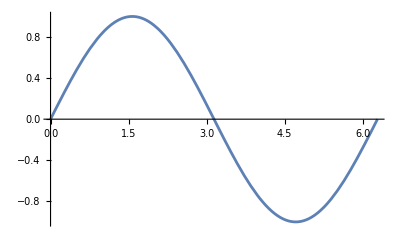

```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

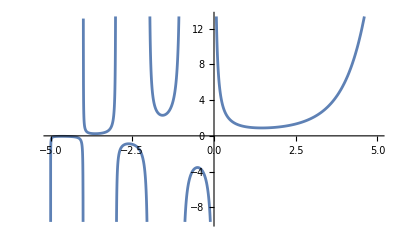

```mathematica
Plot[Gamma[x],{x,-5,5}]
```

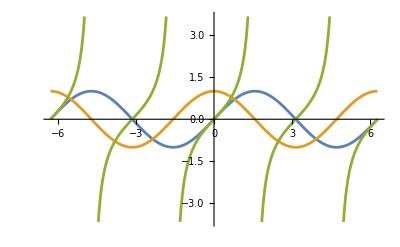

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,-2 Pi,2 Pi}]
```

```mathematica
Plot[Gamma[x],{x,-5,5},PlotRange->{-10,10},PlotLabel->Style[Gamma[x],Black,Bold,16],AxesStyle->Directive[Arrowheads[0.03],Italic,Thick],AxesLabel->(Style[#,Black,Bold,16]&/@{x,y}),ColorFunction->Hue]
```

-Graphics-

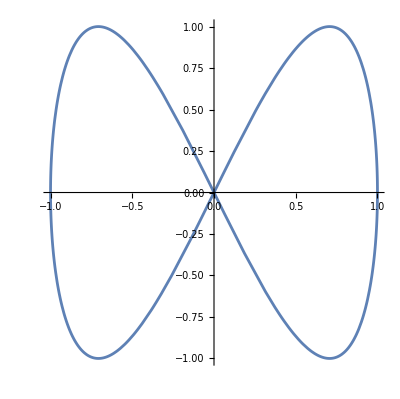

```mathematica
ParametricPlot[{Sin[u],Sin[2 u]},{u,0,2 Pi}]
```

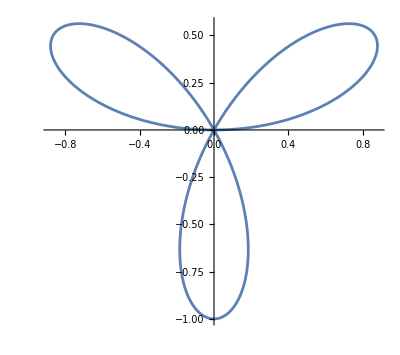

```mathematica
PolarPlot[Sin[3 t],{t,0,Pi}]
```

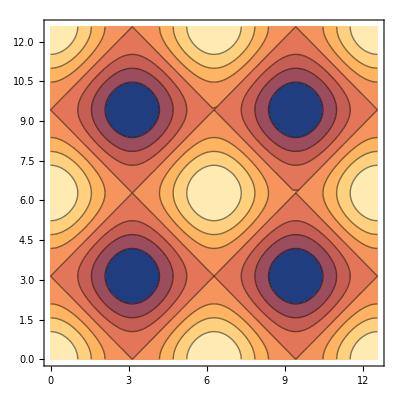

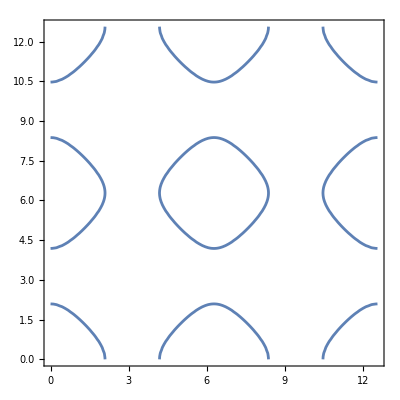

```mathematica
ContourPlot[Cos[x]+Cos[y],{x,0,4 Pi},{y,0,4 Pi}]
ContourPlot[Cos[x]+Cos[y]==1/2,{x,0,4 Pi},{y,0,4 Pi}]
```

```mathematica
DensityPlot[Sin[x] Sin[y],{x,-4,4},{y,-3,3}]
```

-Graphics-

### 2. 三维绘图

```mathematica
Plot3D[Sin[x y],{x,-Pi,Pi},{y,-Pi,Pi}]
```

-Graphics3D-

```mathematica
pic1=Plot3D[Re[Sin[x+I y]],{x,0,5 Pi},{y,0,2},PlotStyle->Green] 
pic2=Plot3D[Im[Sin[x+I y]],{x,0,5 Pi},{y,0,2},PlotStyle->Pink]
Show[pic1,pic2]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[{Re[Sin[x+I y]],Im[Sin[x+I y]]},{x,0,5 Pi},{y,0,2}]
```

-Graphics3D-

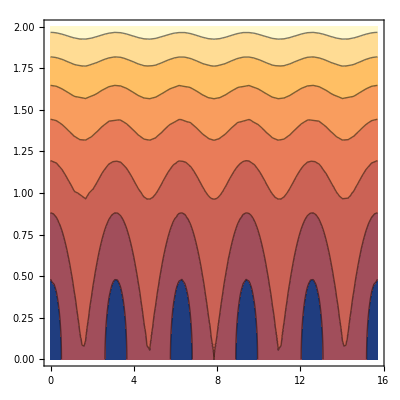

```mathematica
ContourPlot[Abs[Sin[x+I y]],{x,0,5 Pi},{y,0,2}]
```

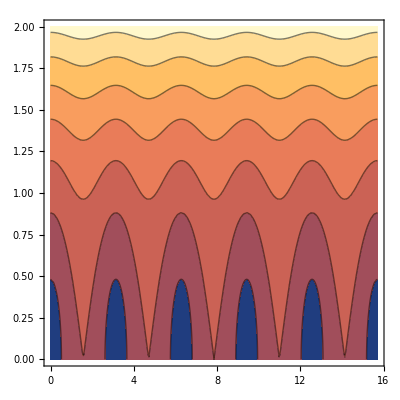

```mathematica
ContourPlot[Abs[Sin[x+I y]],{x,0,5 Pi},{y,0,2},PlotPoints->50]
```

```mathematica
Plot3D[Abs[Sin[x+I y]],{x,0,5 Pi},{y,0,2},ColorFunction->Function[{x,y},Hue[Arg[Sin[x+I y]]/(2 Pi)+1/2]],ColorFunctionScaling->False]
```

-Graphics3D-

```mathematica
ResourceFunction["RiemannSurfacePlot3D"][w==Sqrt[z],Re[w],{z,w}]
```

-Graphics3D-

## 5.Mathematica 中的（偏）微分方程

### 1.符号解

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y''[x]+2 y'[x]+y[x]==0,y[x],x]
```

{{y[x]→ⅇ^-x C[1]+ⅇ^-x x C[2]}}

```mathematica
DSolve[y''[x]+2 y'[x]+y[x]==0,y,x]
```

{{y→Function[{x},ⅇ^-x C[1]+ⅇ^-x x C[2]]}}

```mathematica
y[0]/.%[[1,1]]
```

C[1]

```mathematica
y'[x]/.%%[[1,1]]
```

-ⅇ^-x C[1]+ⅇ^-x C[2]-ⅇ^-x x C[2]

```mathematica
DSolveValue[y''[x]+2 y'[x]+y[x]==0,y,x]
```

Function[{x},ⅇ^-x C[1]+ⅇ^-x x C[2]]

```mathematica
DSolve[{y''[x]+2 y'[x]+y[x]==0,y[1]==1,y'[1]==1},y,x]
```

{{y→Function[{x},ⅇ^(1-x) (-1+2 x)]}}

```mathematica
DSolve[c^2 D[u[x,t],x,x]-D[u[x,t],t,t]==0,u[x,t],{x,t}]
```

{{u[x,t]→C[1][t-x/(√(c^2))]+C[2][t+x/(√(c^2))]}}

```mathematica
Assuming[c>0,DSolve[c^2 D[u[x,t],x,x]-D[u[x,t],t,t]==0,u[x,t],{x,t}]]
```

{{u[x,t]→C[1][t-x/c]+C[2][t+x/c]}}

```mathematica
DSolve[{Laplacian[u[x,y],{x,y}]==0,u[0,y]==y,u[a,y]==0,u[x,0]==0,u[x,b]==0},u[x,y],{x,0,a},{y,0,b}]
```

{{u[x,y]→-(2 (-1)^K[1] b Csch[(a π K[1])/b] Sin[(π y K[1])/b] Sinh[(π (a-x) K[1])/b])/(π K[1])K[1]1∞}}

```mathematica
DSolve[{D[u[x,t],t,t]-c^2 D[u[x,t],x,x]==0,u[x,0]==x (1-x),(D[u[x,t],t]/. t->0)==0,u[0,t]==0,u[1,t]==0},u[x,t],{x,t}]
```

{{u[x,t]→-(4 (-1+(-1)^K[1]) Cos[√(c^2) π t K[1]] Sin[π x K[1]])/(π^3 K[1]^3)K[1]1∞}}

```mathematica
%/.Infinity->5//Activate
```

{{u[x,t]→(8 Cos[√(c^2) π t] Sin[π x])/π^3+(8 Cos[3 √(c^2) π t] Sin[3 π x])/(27 π^3)+(8 Cos[5 √(c^2) π t] Sin[5 π x])/(125 π^3)}}

```mathematica
TruncateSum[%%,5]
```

{{u[x,t]→(8 Cos[√(c^2) π t] Sin[π x])/π^3+(8 Cos[3 √(c^2) π t] Sin[3 π x])/(27 π^3)+(8 Cos[5 √(c^2) π t] Sin[5 π x])/(125 π^3)}}

### 2. 级数解

```mathematica
ode=y''[x]-6 y[x]^2-x==0;
```

```mathematica
init={y'[0]==0,y[0]==1};
```

```mathematica
op=D[#,{x,2}]-6 #^2-x&;
```

```mathematica
ys=Series[y[x],{x,0,5}]
```

y[0]+y'[0] x+1/2 y''[0] x^2+1/6 y^(3)[0] x^3+1/24 y^(4)[0] x^4+1/120 y^(5)[0] x^5+O[x]^6

```mathematica
sol=SolveAlways[Join[{op[ys]==0},init],x]
```

{{y^(4)[0]→72,y^(5)[0]→12,y^(3)[0]→1,y''[0]→6,y'[0]→0,y[0]→1}}

```mathematica
ys/.sol[[1]]
```

1+3 x^2+x^3/6+3 x^4+x^5/10+O[x]^6

```mathematica
ODESeriesSolution[ode_Equal,inits_List,y_,x_,order_:5]:=Block[{ys,equation,sol},ys=Series[y[x],{x,0,order}];
equation=ode/. y->(Evaluate[ys/. x->#]&);
sol=SolveAlways[Join[{equation},inits],x];
ys/. sol//First]

ODESeriesSolution[y''[x]-6 y[x]^2-x==0,{y'[0]==0,y[0]==1},y,x,20]

ODESeriesSolution[y''[x]-6 y[x]^2-x==0,{},y,x,5]
```

1+3 x^2+x^3/6+3 x^4+x^5/10+3 x^6+(6 x^7)/35+(865 x^8)/336+(17 x^9)/105+(9011 x^10)/4200+(62 x^11)/385+(158779 x^12)/92400+(41915 x^13)/288288+(2830511 x^14)/2102100+(1154969 x^15)/9009000+(2903567 x^16)/2802800+(312222809 x^17)/2858856000+(1942038037 x^18)/2470051584+(190148759 x^19)/2089164000+(5770270252343 x^20)/9777287520000+O[x]^21

y[0]+y'[0] x+3 y[0]^2 x^2+1/6 (1+12 y[0] y'[0]) x^3+1/2 (6 y[0]^3+y'[0]^2) x^4+1/10 (y[0]+30 y[0]^2 y'[0]) x^5+O[x]^6

```mathematica
AsymptoticDSolveValue[{ode,init},y[x],{x,0,5}]
```

1+3 x^2+x^3/6+3 x^4+x^5/10

### 3.数值解

```mathematica
Clear["Global`*"]
```

```mathematica
sol=NDSolveValue[{y''[x]+2 y'[x]+y[x]==0,y[1]==1,y'[1]==1},y,{x,1,10}]
```

InterpolatingFunction[…]

```mathematica
sol[2]
```

1.10364

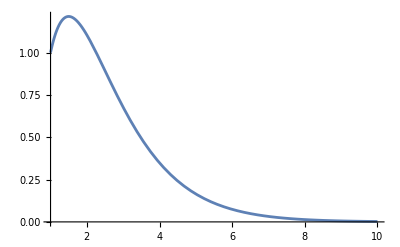

```mathematica
Plot[sol[x],{x,1,10}]
```

```mathematica
sol=NDSolveValue[{D[u[t,x,y],t,t]-Laplacian[u[t,x,y],{x,y}]==0,u[0,x,y]==x y (1-x) (1-y),Derivative[1,0,0][u][0,x,y]==0,DirichletCondition[u[t,x,y]==0,True]},u,{t,0,10},Element[{x,y},Rectangle[{0,0},{1,1}]],Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}}]
```

InterpolatingFunction[{{0., 10.}, {0., 1.}, {0., 1.}}, <>]

```mathematica
list=Table[Plot3D[sol[t,x,y],{x,0,1},{y,0,1},AxesOrigin->{0,0,0},Boxed->False,SphericalRegion->True,PlotRange->{{0,1},{0,1},{-1/12,1/12}}],{t,0,10,0.1}];
ListAnimate[list]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["wave.gif",list]
```

wave.gif